# Tupper's Self-Referential Formula

### Author

Eric W. Weisstein
February 27, 2006

This notebook downloaded from http://mathworld.wolfram.com/notebooks/RecreationalMath/TuppersSelf-ReferentialFormula.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/TuppersSelf-ReferentialFormula.html.

©2006 Wolfram Research, Inc. except for portions noted otherwise

## Formula

```mathematica
Length[IntegerDigits[n=960939379918958884971672962127852754715004339660129306651505519271702802395266424689642842174350718121267153782770623355993237280874144307891325963941337723487857735749823926629715517173716995165232890538221612403238855866184013235585136048828693337902491454229288667081096184496091705183454067827731551705405381627380967602565625016981482083418783163849115590225610003652351370343874461848378737238198224849863465033159410054974700593138339226497249461751545728366702369745461014655997933798537483143786841806593422227898388722980000748404719]]
```

543

### Reduce

#### v5.2

```mathematica
Reduce[1/2<Floor[Mod[Floor[y/17] 2^(-17Floor[x]-Mod[Floor[y],17]),2]]&&0<x<107&&n<y<n+17,{x,y},Integers]
```

False

...wrong...

#### v5.2 Workaround

```mathematica
Length[solns={x,y}/.{ToRules[Reduce[1/2<Floor[Mod[Floor[y/17] 2^(-17Floor[x]-Mod[Floor[y],17]),2]]&&0<=x<=105&&n<=y<=n+16&&(x|y)∈Integers,{x,y}]]}]
```

334

#### v6

```mathematica
Length[solns={x,y}/.{ToRules[Reduce[1/2<Floor[Mod[Floor[y/17] 2^(-17Floor[x]-Mod[Floor[y],17]),2]]&&0<=x<=105&&n<=y<=n+16,{x,y},Integers]]}]
```

```mathematica
Through[{Min,Max}[First/@solns]]
```

{0,105}

```mathematica
Through[{Min,Max}[Last/@solns]]-n
```

{0,16}

```mathematica
Show[Graphics[Rectangle[#,#+1]&/@({105-#[[1]],n-#[[2]]}&/@solns)],AspectRatio->Automatic,PlotRange->All]
```

-Graphics-

### FindInstance

```mathematica
FindInstance[1/2<Floor[Mod[Floor[y/17] 2^(-17Floor[x]-Mod[Floor[y],17]),2]]&&0<x<107&&n<y<n+17,{x,y},Integers]
```

{{x→51,y→960939379918958884971672962127852754715004339660129306651505519271702802395266424689642842174350718121267153782770623355993237280874144307891325963941337723487857735749823926629715517173716995165232890538221612403238855866184013235585136048828693337902491454229288667081096184496091705183454067827731551705405381627380967602565625016981482083418783163849115590225610003652351370343874461848378737238198224849863465033159410054974700593138339226497249461751545728366702369745461014655997933798537483143786841806593422227898388722980000748404726}}

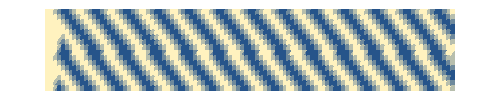

```mathematica
ListDensityPlot[Table[1-Boole[1/2<Floor[Mod[Floor[y/17] 2^(-17Floor[x]-Mod[Floor[y],17]),2]]],{y,n+16,n,-1},{x,105,0,-1}],AspectRatio->Automatic,Mesh->False,ImageSize->500,Frame->False]
```

```mathematica
Boole[1/2 < Floor[Mod[Floor[y/17]*2^(-17*Floor[x] - Mod[Floor[y], 17]), 
      2]]] /. {x -> 0, y -> n}
```

1

```mathematica
n=960939379918958884971672962127852754715004339660129306651505519271702802395266424689642842174350718121267153782770623355993237280874144307891325963941337723487857735749823926629715517173716995165232890538221612403238855866184013235585136048828693337902491454229288667081096184496091705183454067827731551705405381627380967602565625016981482083418783163849115590225610003652351370343874461848378737238198224849863465033159410054974700593138339226497249461751545728366702369745461014655997933798537483143786841806593422227898388722980000748404719
```

960939379918958884971672962127852754715004339660129306651505519271702802395266424689642842174350718121267153782770623355993237280874144307891325963941337723487857735749823926629715517173716995165232890538221612403238855866184013235585136048828693337902491454229288667081096184496091705183454067827731551705405381627380967602565625016981482083418783163849115590225610003652351370343874461848378737238198224849863465033159410054974700593138339226497249461751545728366702369745461014655997933798537483143786841806593422227898388722980000748404719

```mathematica
IntegerDigits[n,2]
```

{1,1,0,1,0,1,1,1,0,0,1,1,0,0,0,0,1,1,0,1,1,0,1,0,1,1,0,1,0,0,1,1,1,1,1,0,0,1,1,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,1,1,1,0,0,0,1,1,1,0,1,1,1,0,0,0,1,1,1,1,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,1,0,0,1,0,1,0,0,1,0,1,1,1,0,1,1,1,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,1,0,1,1,1,0,0,1,0,0,0,0,0,0,0,1,0,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,0,1,1,1,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,0,1,1,1,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,0,1,0,0,0,0,0,1,0,0,0,1,1,1,1,1,1,1,1,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,1,0,1,1,1,0,0,1,0,0,0,0,0,0,0,1,0,0,1,1,1,0,1,0,1,0,1,1,0,0,1,1,1,0,0,1,0,0,0,0,1,1,1,0,1,1,0,1,0,1,1,1,0,0,0,1,1,1,1,0,0,1,0,1,0,0,0,0,0,1,1,0,1,1,1,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1}

```mathematica
binnumber = 10010010010101000100100100101010000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000;
```

```mathematica
n=(2^^11111111111111110100000000000000101000000000000001010000000000000010100000000000000101000000000000001010000000000000010000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000111100000000000010000100000000001000000100000000100000001000000010000000010000001000000001000000100000000100000000100000000100000000100000000100000000100000001000000000100000010000000000100001000000000000111100000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000011111111111111110100000001000000101000000010000001010000000100000010100000001000000101000000101000010001000010001001000001111000001100000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000)*17;ArrayPlot[Table[Boole[1/2<Floor[Mod[Floor[y/17] 2^(-17Floor[x]-Mod[Floor[y],17]),2]]],{y,n,n+16},{x,105,-2,-1}],PixelConstrained->True,Frame->False,ImageSize->1200,PlotRange->{All,All}]
```

-Graphics-

```mathematica
z
```

...bug; shouldn't have to extend to -2...